# 医学生物学分野における高被引用論文の構造的特徴と長期的影響

## 要旨

本研究は、医学生物学分野における高被引用論文の長期的な引用ダイナミクスおよび構造的特徴を明らかにすることを目的とする。従来の計量書誌学では、3年・5年インパクトファクターのような短期的引用指標が主に用いられてきたが、論文の真の影響を把握するには長期的観察が不可欠である。本研究では、単なる被引用数ではなく、引用寿命、雑誌構造、研究テーマ構造といった多層的観点から分析を行った。
データにはPubMed annual baseline (2023) を用い、1946年から2020年までに出版された約3000万件の論文に記載されるレファレンス情報を対象とした。分析手法として、5年間ごとの「累積世代モデル」を構築し、各累積世代の被引用数全体の1%を構成する上位の論文を「高被引用論文」と定義した。また、高被引用論文とそれ以外の論文との比較のために4分位グループを設定した。
論文単位の分析の結果、高被引用論文の中でも最多被引用論文は数十年にわたり引用が持続し、現在までオブソレッセンス（被引用減衰）に至らない長寿命型の論文が存在することが確認された。一方、高被引用論文の中でも被引用減衰が確認された論文では、出版からピークまで約4年、ピークから減衰まで約7年という寿命構造が観察され、生物分野における既存モデルと整合的であった。被引用減衰が確認された論文の階層クラスタリングの結果、明確なタイプ分化は確認されなかった。
雑誌レベルでは、高被引用論文を多く掲載する雑誌が必ずしも高インパクトファクター誌であるとは限らないことが示された。ただし、Kullback–Leibler divergence による分析から、高被引用論文は他グループと比較して特定雑誌への集中傾向（嗜好）が強いことが明らかとなった。
研究テーマ構造の分析では、HeSHディスクリプターを使ったエントロピーの分析から、高被引用論文は他グループと比較して研究テーマが集中的であり、それを引用する論文の研究テーマもまた集中的であることが明らかとなった。一方で研究テーマとそれを引用する論文の研究テーマの間には乖離が見られ、異なる分野から引用されやすい傾向にあることが明らかになった。

## 1. 背景と目的

計量書誌学においては3年インパクトファクターや5年インパクトファクターなど[Cla1]、特定の期間の引用をもとにした指標が多く用いられる。これは一面的には評価の公正性を考慮したものと考えられる。つまり、より古い論文ほど被引用数は多くなり、この「論文の年齢」による効果を差し引くためである。このような視点は雑誌の選定などにおいては重要なものである。一方で、長期に渡る引用の変化を把握することもまた重要である。第一に、前述の公正性における評価期間の設定の根拠となる。次に、短期的には捉えられない累積的な効果を捉えるには真に長期の観察が必要である。また、引用という現象をより深く捉えるためには、単に（被）引用数に着目するだけでなく、引用関係などのこれらの構造的な面へのアプローチが望まれる。本研究では以上のような観点にたち、長期的な引用のダイナミクスを明らかにすることを試みる。

## 2. 関連研究

高被引用論文や引用指標の研究は、近年も幅広い観点から進展している。Liら[Li1]は2300万論文を対象に長期にわたる引用の特徴を分析しグループ構造を明らかにした。また、Yuら[Yu1]は社会心理学分野のトップ被引用論文100本を対象とした構造解析により、主要な出版年・国際協力・ジャーナルの影響構造を明らかにし、被引用論文の研究ネットワーク構造に関する知見を提供している。 雑誌レベルに注目したものとして、Leydesdorff[Le1-4]は雑誌間の関係マップを構築・調査した。天野ら[Am1-2]は医学生物学雑誌の大規模クラスタリングを行い、分野間の引用関係を明らかにした。こうした研究は、高被引用論文あるいはハイインパクト誌がどのような条件下で生まれ、どのような影響経路を持つかをマクロ的視点で捉える試みとして注目される。一方で、論文レベルの被引用性に寄与する構造的因子の体系化も進んでおり、共同研究形態・出版戦略・研究資源配分などの多要因が被引用性に影響する可能性が示唆されている。Hillら[Hil1]は、研究者の研究テーマの転換戦略はむしろその後の影響を減少させる可能性を指摘した。Linら[Lin1]は、被引用論文の全文データを用いて、引用の位置・文脈・引用者との類似性が経時的に変化する現象を観察し、単なる引用数では捉えきれない引用役割の変容を指摘している。Koushaら[Ko1]は、情報科学分野の論文に対し、抄録の「読みやすさ」と論文の「質」が、被引用数にどのように影響するかを調査した。以上紹介した研究は主として被引用性にかかるさまざまな属性の特徴を明らかにするものであるが、高被引用論文に共通する長期的構造特性そのものを多層的に捉える研究は限定的である。本研究は、引用寿命・雑誌構造・テーマ構造（異分野引用）などの要素を統合的に分析することで既存研究とは異なる視点を提供する。

## 3. マテリアル

本研究では、長期的な引用ダイナミクスを把握するため、単年ごとの分析ではなく、引用の累積的効果を反映する「累積世代モデル」を構成する。またPubMedには各論文に統制語（MeSH）が付与されているため、高被引用論文に付与されるMeSHディスクリプターを計量的に分析することにより、研究テーマに関するマクロな構造を見出せると期待される。

### 3.1 データ

本研究では、FTP版のPubMed annual baseline (2023)（以降、PubMedとする）[PM1]を利用する。本研究の対象は、図1に示す1946年から2020年までに出版された論文約3000万件に記載されるレファレンス情報である。

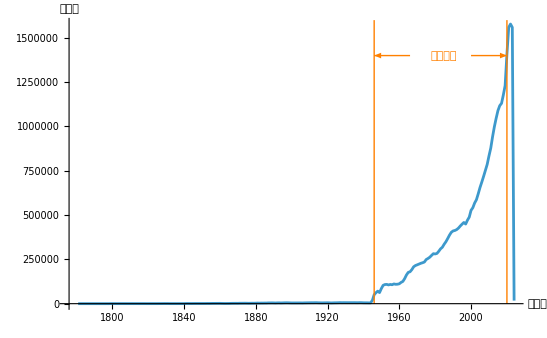

図1

PubMedの登録論文数の推移

### 3.2 累積世代モデルの構成

本研究では、累積的な変化を捉えるために累積的な世代を構成する。まず、1946-2020の出版年をオーバーラップなしの5年ごとの区切りとした15層に分け、これらを累積的に構成する。これを累積世代モデルと称する。構成前の各層の登録論文数、うち参考文献を持つ論文数、引用された論文数、引用数、雑誌数を図2に示す。雑誌数以外は指数関数的な増加を示している。

-Graphics-

図 2

5年ごとの登録論文数

### 3.3 高被引用論文・高被引用論文掲載誌・高被引用テーマ

本研究では、各累積世代において被引用数全体の1%を構成する被引用数上位の論文群を「高被引用論文」と定義する。これらを掲載した雑誌を「高被引用論文掲載誌」、高被引用論文に付与されるMeSHディスクリプターを「高被引用テーマ」と呼ぶ。さらに高被引用論文を引用する論文群を考え、これらの論文に付与されるMeSHディスクリプターを「高被引用論文引用テーマ」とする。また、論文に付与されるMeSHディスクリプター一般を「研究テーマ」、論文を引用する論文に付与されるMeSHディスクリプター一般を「引用テーマ」とする。以上の定義をまとめたものを表1に示す。

表1

本研究での用語定義

高被引用論文 | 被引用数全体の1%を構成する被引用数上位論文。
高被引用論文掲載誌 | 高被引用論文を出版した雑誌。
高被引用テーマ | 高被引用論文に付与されるMeSHディスクリプター。
高被引用論文引用テーマ | 高被引用論文を引用する論文に付与されるMeSHディスクリプター。
研究テーマ | 論文に付与されるMeSHディスクリプター。
引用テーマ | 論文を引用する論文に付与されるMeSHディスクリプター。

### 3.4 比較グループ

のちの章において高被引用論文とその他の論文とを比較するため、高被引用論文を含め全4グループを構成する。前述の高被引用論文をグループ1（G1）とし、同様に被引用数全体を100分した際の上位25-26分位区間にある論文群をG2、50-51分位区間にある論文群をG3、75-76分位区間にある論文群をG4とする。

## 4. 高被引用論文と経年的な引用の効果

### 4.1 高被引用論文の出現

高被引用論文の出現数を図3に示す。高被引用論文数および新規出現高被引用論文数は1946-2010年の累積世代以降に急増しているが、これは近年の収録論文数の急増を受けたものであると思われる。高被引用論文の影響性を確認するため、高被引用論文の全論文に占める割合を図4に示す。被引用数の1%を最大でも全体の0.0035%の論文が構成しており、被引用の集中度の高さが見て取れる。経時変化に一定の傾向はなく緩やかな変動が見られる。高被引用論文の入れ替わりを確認するため、新規高被引用論文の高被引用論文に占める割合を図5に示す。経時変化に一定の傾向は観察されないが、10%から60%の間で順位の入れ替わりが見られる。

-Graphics-

図3

高被引用論文および新規出現高被引用論文の出現数

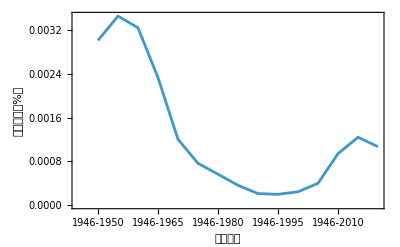

図4

高被引用論文の全論文に占める割合（%）

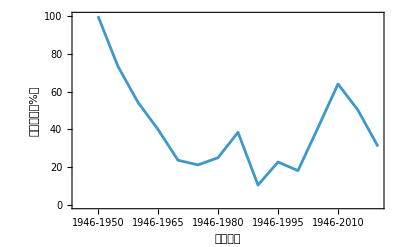

図5

新規出現高被引用論文の高被引用論文に占める割合（%）

### 4.2 最多被引用論文の変遷

各累積世代の最多被引用論文とその被引用数を表2に示す。最多被引用論文は累積世代が進んでも引き続き引用され続ける傾向があり、数十年をかけてインパクトを上昇させている。このため最多被引用論文の交代は少ない。これらはいずれも論文タイトルおよび高被引用テーマを見る限りタンパク質に関するものである。

表2

最多被引用論文タイトル

累積世代 | 高被引用論文タイトル | 高被引用論文掲載誌タイトル | 高被引用テーマ | 被引用数 | 当該累積世代の
高被引用論文数
1946-1950 | Qualitative analysis of proteins: a partition chromatographic method using paper. | The Biochemical journal | - | 74 | 10
1946-1955 | 上記と同じ | 上記と同じ | 上記と同じ | 154 | 30
1946-1960 | Protein measurement with the Folin phenol reagent. | The Journal of biological chemistry | Molybdenum
Phenols
Plant Extracts
Proteins
Tungsten Compounds | 300 | 46
1946-1965 | 上記と同じ | 上記と同じ | 上記と同じ | 1190 | 50
1946-1970 | 上記と同じ | 上記と同じ | 上記と同じ | 3876 | 38
1946-1975 | 上記と同じ | 上記と同じ | 上記と同じ | 9632 | 33
1946-1980 | 上記と同じ | 上記と同じ | 上記と同じ | 17763 | 32
1946-1985 | 上記と同じ | 上記と同じ | 上記と同じ | 25451 | 26
1946-1990 | 上記と同じ | 上記と同じ | 上記と同じ | 32371 | 19
1946-1995 | 上記と同じ | 上記と同じ | 上記と同じ | 37576 | 22
1946-2000 | 上記と同じ | 上記と同じ | 上記と同じ | 40229 | 33
1946-2005 | 上記と同じ | 上記と同じ | 上記と同じ | 42101 | 66
1946-2010 | 上記と同じ | 上記と同じ | 上記と同じ | 44884 | 192
1946-2015 | Cleavage of structural proteins during the assembly of the head of bacteriophage T4. | Nature | Autoradiography
Carbon Isotopes
Coliphages
Electrophoresis, Disc
Genes
Genetics, Microbial
Kinetics
Viral Proteins | 49961 | 315
1946-2020 | 上記と同じ | 上記と同じ | 上記と同じ | 54249 | 336

### 4.3 高被引用論文のオブソレッセンス

章構成

オブソレッセンスベクトルの説明（図）

プロット

クラスごとの指標値：メンバー数、中央値: {A-、A+、Gs、”peakYear”、”len”}

最多被引用論文の統計：{A-、A+、Gs、”peakYear”、”len”}、plot、クラス

ここでは、個別の高被引用論文が長期的にどのように影響を持つかを分析するため、オブソレッセンスに注目し、寿命構造を観察する。まず、オブソレッセンス状態を判定するために、J. Sunらの提案する Obsolescence vector を導入する。Obsolescence vector はGini係数の派生でありO(Gs,A^-)で表されるが、本研究ではO(Gs,A^-,A^+)を用いる。Gsは、小さいほど相対的に引用が早期に偏っていることを示し、|A^-|、|A^+|の値はそれぞれ被引用の減少および増加の変化の速さを示す（図20）。この指標とP.D.B Paroloら、D. Wang らのモデルを勘案し、高被引用論文を次の4クラス（FP/SB/Nm/O）に分類する。うち、クラスNmについてはサブクラスNoを持つ。

FP; Flash in the pan：Sunらは Flash in the pan のモデルとして、Gs=-0.600、A^-=-0.300 を示している。本研究ではこの値を参照し、Gs < -0.600かつA^- < -0.300の値を持つ論文を、Flash in the panと判定した。

SB; Sleeping beauty：SunらはA^+を用いた  Sleeping beauty の基準を示していないが、本研究では Flash in the pan と対照的な条件として Gs > 0.600 かつ A^+ > 0.300の値を持つ論文を Sleeping beautyと判定した。

Nm; 成熟論文：本研究では Flash in the pan にも Sleeping beauty にも含まれない標準的かつある程度引用を得た論文の条件として、 -0.600 > Gs > 0.600 かつ A^- < 0 かつ A^+ > 0 かつ |A^-| > |A^+|  を設定した。

No; 成熟論文のうちオブソレッセンスが確認されるもの：本研究では 成熟論文のうちさらに A^- にかかる条件をより厳しくした A^- < 0 となる論文集合をオブソレッセンスの傾向があるものとした。

O; 上記以外のもの：以上の条件に含まれないものとして被引用が成長中のものや特殊な被引用形状ののものが考えられる。

表6に各クラスの指標値（中央値）を示す。高被引用論文では半数以上がクラスO（成長中と思われるもの）に属し、他のクラスと比べ年齢も低い。なお、クラスFP（Flash in the pan）の年齢が高いのは、早期の高い被引用だけでなくその後の十分な低い被引用期間も要することによる。表7に最多被引用論文の指標値を示す。最多被引用論文は、いずれも高い年齢でああるが、クラスはFPおよびOからなる。

次に、これらの指標値が高被引用論文に特有のものであるかを確認するため、表8にG2論文の指標値を示す。本指標値の算出には十分な被引用数が必要であるため、比較するグループはG2論文のみとした。表によればG1はG2に比べ、年齢は高く、Gsの値が小さいものは少なく、Gsの値が大きいものは多くなる傾向にある。つまり、単なる年齢によるものではない、長期に渡る引用の継続が高被引用をなす一つの要因と推察される。

表6

G1論文の指標値（中央値）

クラス | A^- | A^+ | Gs | 年齢 | メンバー数(%)
FP | -0.346 | 0. | -0.691 | 70. | 29(5)
Nm | -0.166 | 0.005 | -0.323 | 44. | 150(28)
No | -0.192 | 0.004 | -0.374 | 49.5 | 114(21)
SB | 0. | 0.336 | 0.671 | 35. | 30(6)
O | 0. | 0.147 | 0.295 | 17. | 327(61)

表7

最多被引用論文の指標値

"論文タイトル" | "クラス" | "A^-" | "A^+" | "Gs" | "年齢"
"Qualitative analysis of ..." | "FP" | -0.332 | 0. | -0.664 | 77.
"Protein measurement with ..." | "O" | -0.011 | 0.066 | 0.11 | 70.
"Cleavage of structural proteins ..." | "O" | -0.015 | 0.052 | 0.076 | 51.

表8

G2論文の指標値（中央値）

クラス | A^- | A^+ | Gs | 年齢 | メンバー数
(%:G1との比較)
FP | -0.347 | 0. | -0.694 | 51. | 11254(13↑)
Nm | -0.119 | 0.002 | -0.231 | 32. | 36575(41↑)
No | -0.198 | 0.001 | -0.392 | 40. | 20634(23↑)
SB | 0. | 0.324 | 0.648 | 42. | 301(0↓)
O | -0.001 | 0.074 | 0.142 | 19. | 40891(46↓)

図20

Obsolescence vector （Sunらによる）

本研究ではO(Gs,A^-,A^+)を用いてオブソレッセンスの状態を判定する。GsがGini係数に相当するが、Gini係数のローレンツ曲線ではA^-は発生しない。一般的な寿命構造では被引用曲線は対数正規分布型となるため、出版後十分な時間が経過した論文では、A^- > A^+ となる。

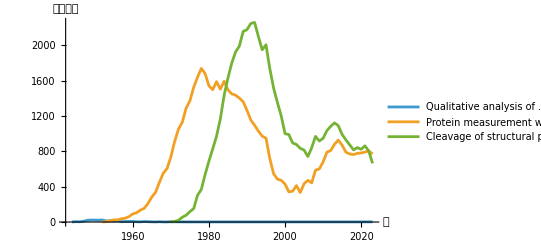

図10

最多被引用論文タイトルの被引用数の推移

括弧内の数字は出版年を示す。3タイトルはいずれも被引用の十分な減衰が確認されなかった。また、うち2タイトルについては多峰性が見て取れる。

## 5. 高被引用論文掲載誌

これまで論文単位で観察してきたが、引用の構造は出版媒体（雑誌）という制度的単位とも深く関係している。そこで次に、論文レベルの現象が雑誌レベルでどのように現れるかを調査する。

### 5.1 高被引用論文掲載誌の出現

高被引用論文掲載誌の出現数を図11に示す。高被引用論文掲載誌数および新規出現高被引用論文掲載誌は1946-2010年の累積世代以降に急増しており、前述した高被引用論文数の急増のタイミングと一致する。高被引用論文掲載誌の影響性を確認するため、高被引用論文掲載誌の全雑誌に占める割合を図12に示す。経時変化に一定の傾向はなく緩やかな変動が観察される。高被引用論文掲載誌の入れ替わりを確認するため、新規出現高被引用論文掲載誌の高被引用論文掲載誌に占める割合を図13に示す。経時変化に一定の傾向は観察されず、かつ、激しい変動が観察される。

-Graphics-

図11

高被引用論文掲載誌および新規出現高被引用論文掲載誌の出現数

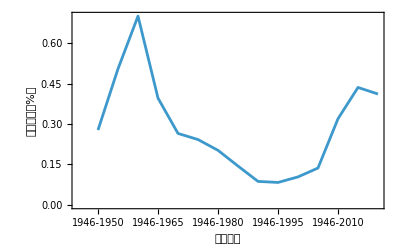

図12

高被引用論文掲載誌の全雑誌に占める割合（%）

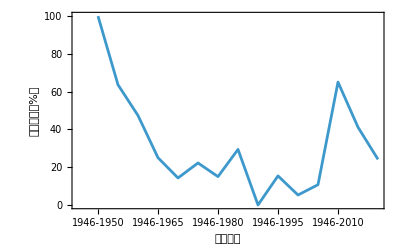

図13

新規出現高被引用論文掲載誌の高被引用論文掲載誌に占める割合（%）

### 5.2 高被引用論文掲載誌の変遷

ここでは高被引用論文掲載誌の変化を高被引用でないグループのそれと比較する。G1-G4の当該論文の掲載数上位の雑誌一覧を表4に示す。各誌のインパクトファクターとその発表年についてはJournal Citation Reports  (JCR）[JCR1]から求めた。JCRではインパクトファクターの公開が1997からであるため、1946-2000年の累積世代以降についてのみ、累積世代の最終年のインパクトファクターを求めた。ここから、高被引用論文を持つ雑誌は必ずしもインパクトファクターが高い雑誌ではないことがわかる。一方、雑誌の構成においてはグループ間に特別な差異を認めらない。そこで、各グループでどの程度の雑誌の嗜好があるかを確認するため、全てのグループを合成した集団と各グループとの間でKullback–Leibler divergence（KLD）を求めたものを図14に示す。図14からは、高被引用論文は他のグループに比べ雑誌の嗜好が強いことが明らかになった。

表4-1

高被引用論文掲載誌のうち最大の論文数を持つもの

累積世代 | 雑誌タイトル | 当該誌の
高被引用論文数 | 当該誌の高被引用論文が
当該累積世代の高被引用論文
全体に占める割合(%) | IF | /IF発表年
1946-1950 | The Journal of clinical investigation
The Biochemical journal | 3
3 | 30 | 12.015/2000 | 15.053/2005 | 14.152/2010 | 12.575/2015 | 14.808/2020
4.28/2000 | 4.224/2005 | 5.016/2010 | 3.562/2015 | 3.857/2020
1946-1955 | The Biochemical journal | 13 | 43 | 4.28/2000 | 4.224/2005 | 5.016/2010 | 3.562/2015 | 3.857/2020
1946-1960 | The Biochemical journal | 11 | 24 | 4.28/2000 | 4.224/2005 | 5.016/2010 | 3.562/2015 | 3.857/2020
1946-1965 | The Biochemical journal | 13 | 26 | 4.28/2000 | 4.224/2005 | 5.016/2010 | 3.562/2015 | 3.857/2020
1946-1970 | The Biochemical journal | 9 | 24 | 4.28/2000 | 4.224/2005 | 5.016/2010 | 3.562/2015 | 3.857/2020
1946-1975 | The Journal of biological chemistry | 7 | 21 | 7.368/2000 | 5.854/2005 | 5.328/2010 | 4.258/2015 | 5.157/2020
1946-1980 | The Journal of biological chemistry | 7 | 22 | 7.368/2000 | 5.854/2005 | 5.328/2010 | 4.258/2015 | 5.157/2020
1946-1985 | The Journal of biological chemistry | 5 | 19 | 7.368/2000 | 5.854/2005 | 5.328/2010 | 4.258/2015 | 5.157/2020
1946-1990 | The Journal of biological chemistry | 4 | 21 | 7.368/2000 | 5.854/2005 | 5.328/2010 | 4.258/2015 | 5.157/2020
1946-1995 | The Journal of biological chemistry | 4 | 18 | 7.368/2000 | 5.854/2005 | 5.328/2010 | 4.258/2015 | 5.157/2020
1946-2000 | Journal of molecular biology
Proceedings of the National Academy of Sciences of the United States of America | 4
4 | 12 | 5.388/2000 | 5.229/2005 | 4.008/2010 | 4.517/2015 | 5.469/2020
10.789/2000 | 10.231/2005 | 9.771/2010 | 9.423/2015 | 11.205/2020
1946-2005 | Proceedings of the National Academy of Sciences of the United States of America | 8 | 12 | 10.789/2000 | 10.231/2005 | 9.771/2010 | 9.423/2015 | 11.205/2020
1946-2010 | Proceedings of the National Academy of Sciences of the United States of America
Nature | 14
14 | 7 | 10.789/2000 | 10.231/2005 | 9.771/2010 | 9.423/2015 | 11.205/2020
25.814/2000 | 29.273/2005 | 36.104/2010 | 38.138/2015 | 49.962/2020
1946-2015 | Nature | 20 | 6 | 25.814/2000 | 29.273/2005 | 36.104/2010 | 38.138/2015 | 49.962/2020
1946-2020 | Bioinformatics (Oxford, England) | 17 | 5 | 3.409/2000 | 6.019/2005 | 4.877/2010 | 5.766/2015 | 6.937/2020

表4-2

G2雑誌のうち最大の論文数を持つもの

累積世代 | 雑誌タイトル | 当該誌の
G2論文数 | 当該誌のG2論文が
当該累積世代のG2論文
全体に占める割合(%) | IF / 発表年
1946-1950 | Journal of bacteriology | 34 | 45 | 3.506/2000 4.167/2005 3.726/2010 3.198/2015 3.49/2020
1946-1955 | The Biochemical journal | 20 | 7 | 4.28/2000 4.224/2005 5.016/2010 3.562/2015 3.857/2020
1946-1960 | The Biochemical journal | 64 | 10 | 4.28/2000 4.224/2005 5.016/2010 3.562/2015 3.857/2020
1946-1965 | The Biochemical journal | 62 | 7 | 4.28/2000 4.224/2005 5.016/2010 3.562/2015 3.857/2020
1946-1970 | The Journal of biological chemistry | 90 | 6 | 7.368/2000 5.854/2005 5.328/2010 4.258/2015 5.157/2020
1946-1975 | The Journal of physiology | 98 | 5 | 4.455/2000 4.272/2005 5.139/2010 4.731/2015 5.182/2020
1946-1980 | The Journal of biological chemistry | 150 | 5 | 7.368/2000 5.854/2005 5.328/2010 4.258/2015 5.157/2020
1946-1985 | Proceedings of the National Academy of Sciences of the United States of America | 214 | 6 | 10.789/2000 10.231/2005 9.771/2010 9.423/2015 11.205/2020
1946-1990 | Proceedings of the National Academy of Sciences of the United States of America | 316 | 7 | 10.789/2000 10.231/2005 9.771/2010 9.423/2015 11.205/2020
1946-1995 | Proceedings of the National Academy of Sciences of the United States of America | 410 | 7 | 10.789/2000 10.231/2005 9.771/2010 9.423/2015 11.205/2020
1946-2000 | Proceedings of the National Academy of Sciences of the United States of America | 490 | 7 | 10.789/2000 10.231/2005 9.771/2010 9.423/2015 11.205/2020
1946-2005 | Proceedings of the National Academy of Sciences of the United States of America | 715 | 7 | 10.789/2000 10.231/2005 9.771/2010 9.423/2015 11.205/2020
1946-2010 | Proceedings of the National Academy of Sciences of the United States of America | 947 | 6 | 10.789/2000 10.231/2005 9.771/2010 9.423/2015 11.205/2020
1946-2015 | Proceedings of the National Academy of Sciences of the United States of America | 882 | 5 | 10.789/2000 10.231/2005 9.771/2010 9.423/2015 11.205/2020
1946-2020 | Proceedings of the National Academy of Sciences of the United States of America | 810 | 3 | 10.789/2000 10.231/2005 9.771/2010 9.423/2015 11.205/2020

表4-3

G3雑誌のうち最大の論文数を持つもの

累積世代 | 雑誌タイトル | 当該誌の
G3論文数 | 当該誌のG3論文が
当該累積世代のG3論文
全体に占める割合(%) | IF / 発表年
1946-1950 | The Biochemical journal | 41 | 24 | 4.28/2000 4.224/2005 5.016/2010 3.562/2015 3.857/2020
1946-1955 | The Journal of biological chemistry | 21 | 4 | 7.368/2000 5.854/2005 5.328/2010 4.258/2015 5.157/2020
1946-1960 | Proceedings of the Society for Experimental Biology and Medicine. 
Society for Experimental Biology and Medicine (New York, N.Y.) | 71 | 5 | 3.415/2000 -/2005 -/2010 -/2015 -/2020
1946-1965 | The Journal of biological chemistry | 72 | 3 | 7.368/2000 5.854/2005 5.328/2010 4.258/2015 5.157/2020
1946-1970 | The Journal of biological chemistry | 116 | 3 | 7.368/2000 5.854/2005 5.328/2010 4.258/2015 5.157/2020
1946-1975 | The Journal of biological chemistry | 205 | 4 | 7.368/2000 5.854/2005 5.328/2010 4.258/2015 5.157/2020
1946-1980 | The Biochemical journal | 267 | 4 | 4.28/2000 4.224/2005 5.016/2010 3.562/2015 3.857/2020
1946-1985 | Proceedings of the National Academy of Sciences of the United States of America | 388 | 4 | 10.789/2000 10.231/2005 9.771/2010 9.423/2015 11.205/2020
1946-1990 | The Journal of biological chemistry | 440 | 4 | 7.368/2000 5.854/2005 5.328/2010 4.258/2015 5.157/2020
1946-1995 | The Journal of biological chemistry | 782 | 5 | 7.368/2000 5.854/2005 5.328/2010 4.258/2015 5.157/2020
1946-2000 | The Journal of biological chemistry | 897 | 5 | 7.368/2000 5.854/2005 5.328/2010 4.258/2015 5.157/2020
1946-2005 | The Journal of biological chemistry | 1419 | 5 | 7.368/2000 5.854/2005 5.328/2010 4.258/2015 5.157/2020
1946-2010 | The Journal of biological chemistry | 1681 | 4 | 7.368/2000 5.854/2005 5.328/2010 4.258/2015 5.157/2020
1946-2015 | The Journal of biological chemistry | 1976 | 4 | 7.368/2000 5.854/2005 5.328/2010 4.258/2015 5.157/2020
1946-2020 | The Journal of biological chemistry | 1678 | 2 | 7.368/2000 5.854/2005 5.328/2010 4.258/2015 5.157/2020

表4-4

G4雑誌のうち最大の論文数を持つもの

累積世代 | 雑誌タイトル | 当該誌の
G4論文数 | 当該誌のG4論文が
当該累積世代のG4論文
全体に占める割合(%) | IF / 発表年
1946-1950 | Annals of surgery | 34 | 10 | 5.987/2000 6.328/2005 7.474/2010 8.569/2015 12.969/2020
1946-1955 | Annals of surgery | 105 | 6 | 5.987/2000 6.328/2005 7.474/2010 8.569/2015 12.969/2020
1946-1960 | The Biochemical journal | 240 | 10 | 4.28/2000 4.224/2005 5.016/2010 3.562/2015 3.857/2020
1946-1965 | Nature | 121 | 3 | 25.814/2000 29.273/2005 36.104/2010 38.138/2015 49.962/2020
1946-1970 | British medical journal | 185 | 2 | 5.331/2000 9.052/2005 13.471/2010 -/2015 -/2020
1946-1975 | Biochimica et biophysica acta | 290 | 3 | -/2000 -/2005 -/2010 -/2015 -/2020
1946-1980 | Biochimica et biophysica acta | 489 | 3 | -/2000 -/2005 -/2010 -/2015 -/2020
1946-1985 | The Journal of biological chemistry | 627 | 3 | 7.368/2000 5.854/2005 5.328/2010 4.258/2015 5.157/2020
1946-1990 | Biochimica et biophysica acta | 842 | 3 | -/2000 -/2005 -/2010 -/2015 -/2020
1946-1995 | The Journal of biological chemistry | 1142 | 3 | 7.368/2000 5.854/2005 5.328/2010 4.258/2015 5.157/2020
1946-2000 | The Journal of biological chemistry | 1770 | 4 | 7.368/2000 5.854/2005 5.328/2010 4.258/2015 5.157/2020
1946-2005 | The Journal of biological chemistry | 1375 | 2 | 7.368/2000 5.854/2005 5.328/2010 4.258/2015 5.157/2020
1946-2010 | The Journal of biological chemistry | 2093 | 2 | 7.368/2000 5.854/2005 5.328/2010 4.258/2015 5.157/2020
1946-2015 | PloS one | 3117 | 2 | -/2000 -/2005 4.411/2010 3.057/2015 3.24/2020
1946-2020 | PloS one | 3560 | 2 | -/2000 -/2005 4.411/2010 3.057/2015 3.24/2020

-Graphics-

図14

各グループの雑誌の構成に関するKLD

## 6. 高被引用テーマ

以上のように、出版という観点からは各グループに明確な特徴を見出せないものの、高被引用論文は高被引用でない論文に比べ雑誌の嗜好が強いことがわかった。ここでは、視点を変え、研究内容に関する構造的な差を明らかにするため、論文のテーマに着目する。

### 6.1 高被引用テーマの出現

高被引用テーマのユニーク出現数を図15に示す。2023年MeSHディスクリプターの総数はおよそ30000であるが、各累積世代における高被引用テーマの出現数は最大でも3000を超える程度であり高被引用テーマには集中が見られる。高被引用テーマの入れ替わりを確認するため、新規出現高被引用テーマの高被引用テーマ全体に占める割合を図16に示す。経時的に一定の傾向は観察されず、数%から十数%の範囲での入れ替わりが観察される。なお、1946-1955年の累積世代に高い値が見られる理由は、前累積世代ではMeSHディスクリプターの付与がほとんどなかったためである。

-Graphics-

図15

高被引用論文に付与された高被引用テーマの種数

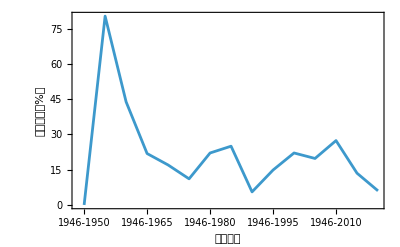

図16

新規出現高被引用テーマの高被引用テーマ全体に占める割合（%）

### 6.2 高被引用テーマの変遷

ここでは高被引用テーマの変化を、高被引用でない論文の研究テーマ（または引用テーマ）と比較する。
各累積世代、各グループごとの最頻出研究テーマと引用テーマを表5に示す。これらのうちG1の研究テーマ（高被引用テーマ）にのみにバラエティが確認される。
次に、各累積世代の研究テーマと引用テーマの多様性を見るために各グループのエントロピーの変化を観察した。研究テーマ、引用テーマ、研究テーマと引用テーマ対の出現数のエントロピーを、それぞれ図17に示す。計数の方法は研究テーマと引用テーマはそれぞれ論文ごとの分数カウントを採用する。研究テーマ対引用テーマのペアについては、ひとつの参照ごとに研究テーマと引用テーマの2部グラフを構成し、エッジの重みの合計が1となる分数カウントを採用する。図17からは高被引用論文グループのみがエントロピーが低く、その他のグループ間ではそれほど差がないことがわかる。なお、1946-1950年の累積世代に関してはMeSHディスクリプターの付与数が十分でなかったため除外している。
また、研究者の引用行動は必ずしも当該論文と同じテーマを引用するものではない。この転換の程度を見るために、グループごとに研究テーマと引用テーマのコサイン距離を観察した。この結果を図18に示す。こちらも高被引用グループのみが他とは異なる様相を示した。また、高被引用グループは1946-2010年の累積世代以降、転換の程度は減少傾向にあり、他のグループとの差はなくなりつつあるように推察される。
さらに、各累積世代間に対して研究テーマの転換の程度を確認するために、各グループの累積世代間の研究テーマのコサイン距離を観察した。累積世代間では論文集合のメンバーが異なるので論文集合全体のテーマの重み付カウントを用いた。この結果を図19に示す。これによれば累積世代間のテーマの転換の程度は一定の傾向を示さなかったが、グループ2のみが常に低い転換の程度を保っている。
以上より、高被引用論文には次の特徴があると考えられる：(1)高被引用論文は異なるテーマから引用されやすい。このことは表6の最頻出テーマから予想され、図18に示す転換の程度もこれを裏付けている。(2)高被引用論文は研究テーマが集中的であり、それを引用する論文の研究テーマもまた集中的である。このことは図17から示唆される。(3)高被引用論文のテーマの多様性は、共時的には低いが通時的には必ずしも低くないと思われる。このことは、図17では他のグループに比べ低いエントロピーが観察されるにもかかわらず、図19では他のグループと変わらない程度の転換が観察されることから推察される。

表5

累積世代ごと論文グループごとの最頻出テーマ

1946-1955
1946-1960
1946-1965
1946-1970
1946-1975
1946-1980
1946-1985
1946-1990
1946-1995
1946-2000
1946-2005
1946-2010
1946-2015
1946-2020 | G1
引用テーマ | 
研究テーマ
Humans | Insulin
Humans | Blood Proteins
Animals | Microscopy, Electron
Animals | Microscopy, Electron
Animals | Microscopy, Electron
Animals | Proteins
Animals | Proteins
Animals | Proteins
Animals | Base Sequence
Animals | Base Sequence
Animals | Base Sequence
Animals | Humans
Humans | Humans
Humans | Humans | G2
引用テーマ | 
研究テーマ
Humans | Humans
Humans | Humans
Humans | Humans
Humans | Humans
Humans | Humans
Humans | Humans
Animals | Humans
Animals | Animals
Animals | Humans
Animals | Animals
Humans | Animals
Humans | Humans
Humans | Humans
Humans | Humans | G3
引用テーマ | 
研究テーマ
Humans | Humans
Humans | Humans
Humans | Humans
Humans | Humans
Humans | Humans
Humans | Humans
Humans | Animals
Humans | Humans
Humans | Humans
Humans | Humans
Humans | Humans
Humans | Humans
Humans | Humans
Humans | Humans | G4
引用テーマ | 
研究テーマ
Humans | Humans
Humans | Humans
Humans | Humans
Humans | Humans
Humans | Animals
Humans | Humans
Humans | Humans
Humans | Humans
Humans | Humans
Humans | Humans
Humans | Humans
Humans | Humans
Humans | Humans
Humans | Humans

-Graphics--Graphics--Graphics-

図17

累積世代、論文グループごとの研究テーマの出現に関するエントロピー

1946-1950年の累積世代では十分なMeSHディスクリプターの付与がなかったため対象外とした。

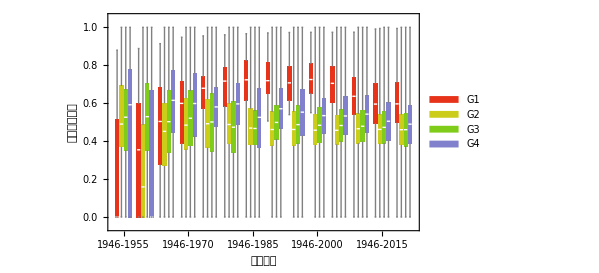

図18

累積世代、論文グループごとの研究テーマに対する引用テーマの転換の程度

箱ひげ図の区間は、下から最小値、25%分位点、中央値、75%分位点、最大値となる。1946-1950年の累積世代では十分なMeSHディスクリプターの付与がなかったため対象外とした。

-Graphics-

図19

論文グループごとの累積世代間の研究テーマの転換の程度

1946-1950年の累積世代では十分なMeSHディスクリプターの付与がなかったため対象外とした。

## 7. まとめ

高被引用論文の順位変化とオブソレッセンス

高被引用論文はその被引用の累積的な効果により長期にわたり上位の順位を維持するものの、最終的には被引用の十分な減衰が確認され、新しい累積世代の論文にその座を明け渡す現象を確認できた。この交代までの被引用の累積的な効果には非常に長いものが多く最長で50年以上であった。一方、被引用の十分な減衰が観察された論文群の、被引用数変化の特徴（出版から被引用のピークまでのモードや被引用の長期変化の形状）は過去の報告を裏付けるものであった。ただし、被引用の十分な減衰が確認されない論文も存在し、これらは出版から被引用のピークがより長期になる傾向が見られ、最上位の論文はこの傾向にある。

高被引用論文掲載誌の特徴

長期にわたる引用を考慮した、本研究の定義による高被引用論文は、必ずしも高いインパクトファクターの雑誌に掲載されるわけではないことが明らかになった。高被引用論文掲載誌は、インパクトファクターを見れば3-50と幅広い。一方、G2-G4の雑誌群では3-10程度でありインパクトファクターの高い雑誌は確認されなかった。また、実際にはよりインパクトファクターが高い雑誌が存在するにもかかわらず、本研究では被引用最上位の論文においてそのような雑誌の出現を確認できなかった。

高被引用テーマと高被引用論文引用テーマ

高被引用論文は、研究テーマは集中的であるが、異なるテーマの論文から引用されやすいことが明らかになった。高被引用論文は、研究テーマおよび引用テーマそれぞれを個別に見た場合の多様性は低いが、研究テーマ対引用テーマの転換という観点では転換の程度が高くなる。もしこれがオブソレッセンスに影響しているのだとすれば、様々な研究領域から興味を持たれるようなテーマの論文は”長生き”するのかもしれない。前述の雑誌の特徴に照らせば、高被引用論文掲載誌に、幅広い領域から興味を持たれるであろう基礎領域や学際的分野の雑誌が見られる一方で、医学や医工学といった特定の応用領域の雑誌が見られないことも、これを示唆している。

長期的な傾向

研究テーマ/引用テーマの多様性（エントロピー）はすべてのグループで経時的に上昇傾向にあり、高被引用論文のみが他と比べて低い。研究テーマ対引用テーマの転換の程度はいずれのグループでも経時的に安定しているが、高被引用論文のみにやや異なる挙動が見られる。累積世代間の研究テーマの転換の程度は安定しておらず、特段の傾向は観察されなかった。高被引用論文/高被引用論文掲載誌/高被引用テーマの新規出現割合、つまり順位の入れ替わりの程度は安定しておらず、特段の傾向は観察されなかった。

## 参考

[Am1] 天野晃;児玉閲;柴田大輔;小野寺夏生. 引用データに基づく自然科学領域における学術研究分野間の関係. 情報メディア研究. 2013, Vol 12, No. 1, p. 28-41.

[Am2] 天野晃;児玉閲. 引用にもとづく雑誌クラスタリング法の開発. 情報メディア研究. 2008, Vol 7, No. 1, p. 63-73.

[Cla1] The Clarivate Impact Factor. https://clarivate.com/academia-government/essays/impact-factor . (accessed 2025.07.01)

[Hil1] Ryan Hill, Yian Yin, Carolyn Stein, Xizhao Wang, Dashun Wang, Benjamin F. Jones. The pivot penalty in research. Narure. 2025, Vol. 642, p. 999-1006.

[JCR1] Journal Citation Reports. https://jcr.clarivate.com/jcr/home . (accessed 2024.07.01)

[Ko1] Kayvan Kousha, Mike Thelwall. Factors associating with or predicting more cited or higher quality journal articles: An Annual Review of Information Science and Technology (ARIST) paper. Journal of Association for Information Science and Technology. 2024. Vol. 75 No. 3, p. 215-244.

[Le1] Leydesdorf, L. Various methods for the mapping of science. Scientometrics. 1987, Vol. 11, Nos 5-6, p. 295-324.

[Le2] Leydesdorf, L. Clusters and maps of science journals based on bi-connected graphs in Journal Citation Reports. Journal of Documentation. 2004, Vol. 60, No. 4, p. 371-427.

[Le3] Leydesdorf, L. Indicators of structual change in the dynamics of science: Entropy statisitics of the SCI Journal Citation Re- ports. Scientometrics. 2002, Vol. 53, No. 1, p. 131-159.

[Le4] Leydesdorf, L. Can scientific journals be classified in terms of aggregated journal- journal citation relations using the Journal Citation Reports?. Journal of the American Society for Information Science and Technology. 2006, Vol. 57, No. 5, p. 601-613.

[Li1] Xin Li, Xuli Tang. How biomedical papers accumulated their clinical citations: a large-scale retrospective analysis based on PubMed. arXiv. 2024. 
https://doi.org/10.48550/arXiv.2404.01072

[Lin1] Gege Lin, Nees Jan van Eck, Haiyan Hou, Zhigang Hu. The changing role of cited papers over time: An analysis of highly cited papers based on a large full-text dataset. ArXiv. 2025, https://doi.org/10.48550/arXiv.2509.04190

[Par1] Pietro Della Briotta Parolo and Raj Kumar Pan and Rumi Ghosh and  Bernardo A. Huberman  and Kimmo Kaski and Santo Fortunato. Attention decay in science. Journal of Informatics. 2015. Vol.9, p.734-745.

[PM1] PubMed https://pubmed.ncbi.nlm.nih.gov/ . (accessed 2025.07.01)

[Yu1] Shu Yu, Ke Chen. A bibliometric and altmetric analysis of the top 100 most cited articles in social psychology (2000–2024).  Discover Psychology. 2006, Vol. 6 No. 28. https://doi.org/10.1007/s44202-025-00557-8

[Wan1] Dashun Wang, Chaoming Song, Albert-László Barabási. Quantifying Long-Term Scientific Impact. Science. 2013. Vol. 342, No. 6154. p. 127-132. DOI: 10.1126/science.1237825

Jianjun Sun • Chao Min • Jiang Li, A vector for measuring obsolescence of scientific articles. Scientometrics (2016) 107:745–757. DOI 10.1007/s11192-016-1884-7